```mathematica
Remove["Global`*"];
```

Remove::rmnsm: There are no symbols matching "Global`*".

# 有键盘就行的复变函数

author: 凉凉

简单的 MMA 介绍, 旨在快速地安利 MMA.

## 复数的运算

## 基本的运算和输入

打开一个 MMA 窗口, 输入 (一般乘号可以省略):
通过在 Cell 中按下 Shift-Enter 来运行代码.

```mathematica
(1 + 2 * I)^4
```

-7-24 ⅈ

当然, 通过使用 ESC ... ESC 的方式, 可以让你输入特殊的 Unicode, 或者是嵌入 LATEX 的公式.

```mathematica
π (* ESC pi ESC *)
ⅈ (* ESC ii ESC *)
```

π

ⅈ

广为人知的小技巧:

竖式分号□/□: 通过 C-/ 即同时按下 Ctrl 和 / 键

指数 □^□: 通过 C-^ 即同时按下 Ctrl 和 Shift 和 6 键

## 函数

在MMA中, 一个函数的调用可能如下所示:

```mathematica
Abs[3+4*I]
Arg[1+Sqrt[3]*I]
```

5

π/3

也可能是这样:

```mathematica
Re[Sin[15 * Degree]]//N
```

0.258819

## 代数基本定理

农民版本: 多项式在复数域下有解, 可以分解为 的形式.

定义一个多项式: expf, 并将其分解: (;结尾表示不输出)

```mathematica
expf = (z^8-1)(z^3+8);
Factor[expf]
```

(-1+z) (1+z) (2+z) (1+z^2) (4-2 z+z^2) (1+z^4)

在MMA中, 默认是在复数域计算的, 不过也可以通过 Assuming 来添加限定条件, 限制运算的域之类的.

```mathematica
Refine[Sqrt[x^2]]
Assuming[x>0,Refine[Sqrt[x^2]]]
```

√(x^2)

x

## 极限与微积分

## 极限

```mathematica
Limit[Sin[x]/x,x->0]
```

1

当然, 对于非奇点部分, 使用 Replace 或者缩写 /. 可以将值带入表达式:

```mathematica
Sin[x]/x/.x->1
amp*Sin[w * t]/.{amp->1,w->2*Pi,t->0.3}
```

Sin[1]

0.951057

## 微分和积分

在 MMA 中, 所有的导数都可以认为是偏微分. 毕竟没什么区别.

```mathematica
D[1/(1-z^2),z]
```

(2 z)/((1-z^2)^2)

于是不妨来验证一下 C-R 条件在 x-y 坐标系下的表现:
通过 f[arg_<TYPE>] := <exp> 的方式来定义函数表达式.

```mathematica
testCRCondition[u_,v_]:=And[D[u,x]==D[v,y],D[u,y]==-D[v,x]];
testCRCondition[x^2-y^2,2*x*y]
```

True

以及检测是否是调和函数: (x-y 坐标系)

```mathematica
testHolomorphic[f_]:=
Assuming[x∈Reals&&y∈Reals,
D[f,{x,2}]+D[f,{y,2}]==0];
testHolomorphic[(x+I*y)^2]
testHolomorphic[Re[x+I*y]]
```

True

-Im''[y]+Re''[x]==0

于是对于一个简单的调和函数, 可以求得其对应的 “另一半”:

```mathematica
expu=Exp[x] Sin[y];
testHolomorphic[expu]
```

True

确认过为调和函数, 使用 C-R 条件计算得到:

```mathematica
expDvDx=D[expu,y];
expDvDy=-D[expu,x];
```

利用普通的路径积分即可得到: (% 为上一次计算的结果, 同理还可以用 %<num> 来得到 Out[<num>] 的计算结果.

```mathematica
Integrate[expDvDx,x];
expv=Integrate[expDvDy-D[%,y],y]+%
```

ⅇ^x Cos[y]

不过一般可能更喜欢用这样的方式:

```mathematica
DSolve[{
D[v[x,y],x]==expDvDx,
D[v[x,y],y]==expDvDy
},v[x,y],{x,y}]
```

{{v[x,y]→C[1]+ⅇ^x Cos[y]}}

## 幂级数展开

算一个级数: 在原点展开到5次项

```mathematica
Series[Exp[z],{z,0,5}]
```

1+z+z^2/2+z^3/6+z^4/24+z^5/120+O[z]^6

对于洛朗级数, 实际上可以看作是将 z -> 1/u 进行一个替换后再进行一个展开. (双边展开)
不过为何要如此繁琐呢?

```mathematica
Series[1/(z^2(z-1)),{z,0,2}]
```

-1/z^2-1/z-1-z-z^2+O[z]^3

## 留数定理

柯西定理: 对解析函数有:

留数定理: 构造一个回路绕开所有的瑕点, 对瑕点特殊关照一下, 做一个半径无穷小的一个回路包围瑕点, 该回路的积分即洛朗级数的  项. 于是可以得到留数定理:

所有留数的和为 0, 这个可以用来计算本性奇点或者懒得算的奇点.

柯西公式: 在柯西定理的基础上, 构造有瑕点的  表达式, 并通过留数定理即可知, 积分为

首先是找到函数的奇点:

```mathematica
FunctionPoles[Exp[z]/(1+z),z]
```

{{-1,1}}

```mathematica
FunctionPoles[1/(z^3-z^5),z]
```

{{-1,1},{0,3},{1,1}}

发现在  处有一个 1 阶奇点. 当然实际上在无穷远处还有一个本性奇点. 可以用留数和为 0 来得到.

```mathematica
Residue[Exp[z]/(1+z),{z,-1}]
```

1/ⅇ

当然, 你可能也想要将这些函数整合在一起, 通过一个函数来调用. 那么这个时候, 你可能需要了解一些关于 MMA 中的一些类型以及对应的方法. 
比如, 在上面的 FuctionPoles 的返回值, 用一个花括号括起来的是什么东西? 
以及, 该怎么处理得到的这些东西?

首先, 在 MMA 中, 用一个花括号括起来的是一个 List:

```mathematica
List[1,2,3,4]
```

{1,2,3,4}

你可以通过使用 Part 函数来得到一个 List 的第几个元素. 不过和一般编程不同的是, MMA的第一个元素就是是第一个元素. (不是第零开始的计数就是了)

```mathematica
{1, 2, 3}[[1]]
```

1

当然, 与其用 For 历遍所有的元素, 不如通过 Map 来对一个列表进行处理:

```mathematica
funcPolesAndRes[f_,z_]:=Map[
({#[[1]],Residue[f,{z,#[[1]]}],#[[2]]})&,
FunctionPoles[f,z]];
```

```mathematica
funcPolesAndRes[z/((z-1)(z-2)^2),z]
```

{{2,-1,2},{1,1,1}}

其中, (...)&  的形式构造了一个匿名函数, 通过 # 来访问传入的参数. 这样的匿名函数的好处就是方便:

```mathematica
Table[i,{i,0,5}]
%//(#^2)&
```

{0,1,2,3,4,5}

{0,1,4,9,16,25}

于是就可以拿它来计算回路积分了.

## 傅立叶分析和拉普拉斯变换

傅立叶展开: 将函数扔到基底为三角函数的正交空间里面

傅立叶变换: 将函数变换到连续的频率空间里面 (感觉表达不严谨, 等一个数学系的来纠正)

拉普拉斯变换: 在傅立叶变换的基础上, 对于那些死不收敛的函数, 乘以一个收敛因子  后强制收敛, 然后进行傅立叶变换.

## 傅立叶分析

把一个函数展开成傅立叶级数:
f(x)==a_0/2+∑a_k cos kπx/l+b_k sin kπx/l
其中: 
a_k==1/(δ_k l)∫_-l^l f(x)cos kπx/l dx, δ_k==2 iff k==0 else 1
b_k==1/l∫_-l^l f(x)sin kπx/l dx

```mathematica
akOfFourier[f_,t_,k_,l_]:=
1/(l*If[k==0,2,1])Integrate[f*Cos[(k*π *t)/l],{t,-l,l}];
bkOfFourier[f_,t_,k_,l_]:=
1/l Integrate[f*Sin[(k*π *t)/l],{t,-l,l}];
```

其中, 定义使用了一个 If 用来判断 k 是否为 0. 如果是零的话, 就输出 2, 否则为 1.

```mathematica
akOfFourier[Abs[Sin[x]],x,k,π/2];
%//Assuming[k∈Integers,Refine[#]]&
%//Assuming[k>0,Refine[#]]&
```

-4/((-1+4 k^2) π If[k==0,2,1])

-4/((-1+4 k^2) π)

当然, 如果你不想要编程的话, 可以用现成的函数:

```mathematica
FourierCosSeries[Abs[Sin[x]],x,5]
```

2/π-(4 Cos[2 x])/(3 π)-(4 Cos[4 x])/(15 π)

```mathematica
FourierSinSeries[x,x,5]
```

-2 (-Sin[x]+1/2 Sin[2 x]-1/3 Sin[3 x]+1/4 Sin[4 x]-1/5 Sin[5 x])

害怕展开的不太对? 画个图检查一下:

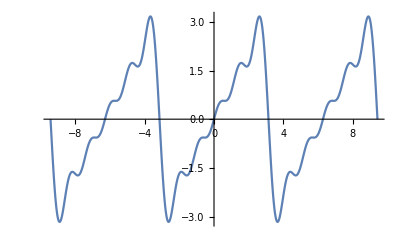

```mathematica
FourierSinSeries[x,x,5]//Plot[#,{x,-3π,3π}]&
```

## 傅立叶变换和拉普拉斯变换

将时域的函数变成频域的函数:

```mathematica
FourierTransform[HeavisideTheta[t],t,ω]
```

ⅈ/(√(2 π) ω)+√(π/2) DiracDelta[ω]

其中, HeavisideTheta 为 Heaviside 函数:

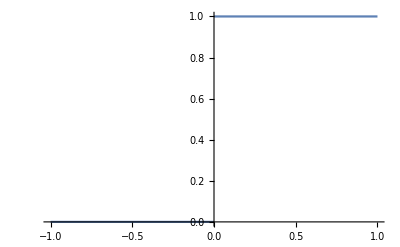

```mathematica
Plot[HeavisideTheta[t],{t,-1,1}]
```

当然, 不能少了逆变换:

```mathematica
FourierTransform[DiracDelta[t],t,ω]
InverseFourierTransform[%,ω,t]
```

1/(√(2 π))

DiracDelta[t]

注: 在 MMA 中, 自带的函数的命名(一般)都非常有规律.

同理还有拉普拉斯变换:

```mathematica
LaplaceTransform[Sinh[ω*t],t,p]
```

ω/(p^2-ω^2)

以及逆变换:

```mathematica
InverseLaplaceTransform[%,p,t]
```

Sinh[t ω]